# Init data

```mathematica
PRECISION=10;
ε = 10^-PRECISION;
f[x_] := Sin[x^2]+Cos[x^2]-10x;
polinom[x_] = x^6+(5 x^5)/8-(85 x^4)/64-(297 x^3)/512+(167 x^2)/512-(23x)/512+1/512;
```

# Method of dichotomy

```mathematica
dichotomiesMethod[func_, start_, end_,plotGraph_] := Module[{x1=start, x2=end,Results={start}},

While[Abs[func[x1]]>ε,
If[x1>x2 || func[x1]func[x2]>0, Return[]];
If[func[(x2 + x1)/2]func[x1] < 0, 
x2=(x2 + x1)/2, x1=(x2 + x1)/2];
Results=Append[Results,(x2+x1)/2];
];
If[plotGraph,Print[ListLinePlot[Results,PlotRange->All]]];
Return[(x2+x1)/2];
];
```

# Method of simple iteration

```mathematica
simpleIterationMethod[func_, start_, stop_,plotGraph_]:= Module[{Results={start},iter=0,maxIters=10000,τ=`0.1,x=start},

While[Abs[func[x]]>ε, 
x+=τ func[x];
Results=Append[Results,x];
iter+=1;
If[iter>maxIters || x>stop||x<start,Return[]];
];
If[plotGraph,Print[ListLinePlot[Results,PlotRange->All]]];
Return[x];
]
```

# Method of tangents

```mathematica
tangentsMethod[func_, start_, stop_,plotGraph_]:= Module[{Results={start},iter=0,maxIters=10000,x=start},
While[Abs[func[x]]>ε, 
x-= func[x]/func'[x];
Results=Append[Results,x];
iter+=1;
If[iter>maxIters || x>stop||x<start,Return[]]
];
If[plotGraph,Print[ListLinePlot[Results,PlotRange->All]]];
Return[x];
]

getDerivative[func_,x_,h_]:=(func[x+h]-func[x-h])/(2h);
k[i_]:=If[i==1,1/3,If[i==2,2/3,1]];
tangentsMethoModificate[func_,start_,stop_,plotGraph_]:=Module[{Results={start},iter=0,maxIters=10000,x=start,δ=10^-16,h=10^-14,mult=1,q},
While[Abs[func[x]]>ε, 
x-= func[x]/getDerivative[func,x,h];
Results=Append[Results,x];
If[Length[Results]>=3,q=(Results[[-1]]-Results[[-2]])/(Results[[-2]]-Results[[-3]]);mult=Round[1/(1-q)]];
h=δ^(1/3)Abs[Results[[-1]]-Results[[-2]]]^k[mult];
iter+=1;
If[iter>maxIters || x>stop||x<start,Return[]]
];
Print["Root ", NumberForm[N[x],PRECISION]," have multiplicity ", mult];
If[plotGraph,Print[ListLinePlot[Results,PlotRange->All]]];
Return[x];
]
```

# Calculating multiplicity

```mathematica
getMultiplicity[func_, x_]:= Module[{mult = 1},
While[Abs[Derivative[mult][func][x]]<=√(√ε), mult+=1];
Return[mult];
]
```

# Getting intervals for roots

```mathematica
getIntervalsRoot[func_,start_, stop_]:=Module[{Results={},h=0.01},
For[x=start, x<=stop,x+=2h,
If[func[x-h]func[x+h]<=0 , Results=Append[Results, {x-h, x+h}],
If[  func'[x-h]func'[x+h]<=0, Results=Append[Results, {x-h, x+h}]];
];
];
Return[Results];
]
```

# Result method of dichotomy

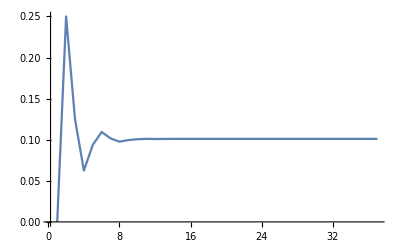

0.1010151829

```mathematica
answ = NumberForm[N[dichotomiesMethod[f, 0, 1,True]], PRECISION]
```

# Result method of simple iterations

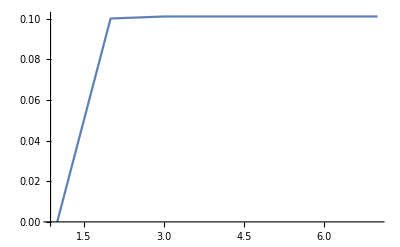

0.1010151829

```mathematica
answ = NumberForm[N[simpleIterationMethod[f, 0, 1,True]], PRECISION]
```

# Result method of tangents

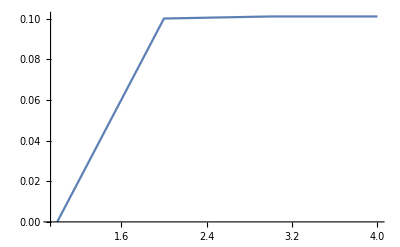

0.1010151829

Root 0.101015 have multiplicity 1

-Graphics-

0.1010151829

```mathematica
answ = NumberForm[N[tangentsMethod[f,0,1,True]], PRECISION]
answ = NumberForm[N[tangentsMethodModificate[f,0,1,True]], PRECISION]
```

```mathematica
intervals=getIntervalsRoot[polinom, -10, 10]
```

{{-1.01,-0.99},{-0.59,-0.57},{0.11,0.13},{0.81,0.83},{0.99,1.01}}

```mathematica
Results={};
For[i=1,i<=Length[intervals],i+=1, 
answ=tangentsMethodModificate[polinom,intervals[[i]][[1]], intervals[[i]][[2]],False];
If[!(answ===Null), Results=Append[Results, answ]];
];
Print[Results]
```

Root -1.000003335 have multiplicity 2

Root 0.1246136238 have multiplicity 3

Root 1. have multiplicity 1

{-1.,0.124614,1.}

```mathematica
For[i=1,i<=Length[Results],i+=1,
Print["Root ", Results[[i]]," have multiplicity ", getMultiplicity[polinom, Results[[i]]]];
]
```

Root -1. have multiplicity 2

Root 0.124564 have multiplicity 3

Root 1. have multiplicity 1

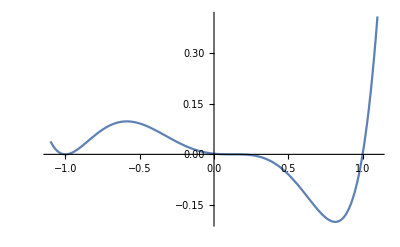

```mathematica
Plot[polinom[x],{x,-1.1, 1.1}]
```

```mathematica
getMultiplicity[polinom, 1/8]
```

3

```mathematica
polinom[0.12456168727246021]
```

9.32276×10^-11